```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY182_cloudy/sec_int_data/610nm.dat"]
```

{{1.83648,0.159138},{1.67469,0.224263},{1.55096,0.234281},{1.77833,0.196142},{1.08395,0.347059},{1.0884,1.7277},{1.10777,0.303949},{1.1184,0.322591},{1.90886,0.139501}}

1.4647-0.724656 x

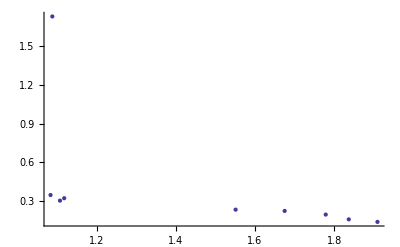

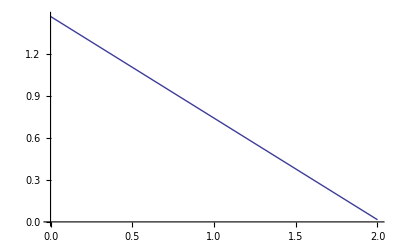

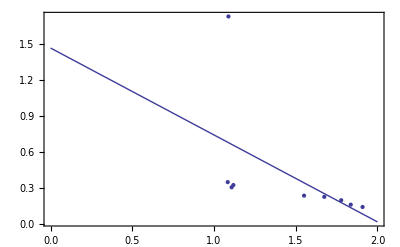

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```